-Graphics-

King Fahd University of Petroleum and Minerals
Civil & Environmental Engineering Department
CE625  (231)  - Mechanics of Composite Materials



SSFF Symmetric Plate under Uniform Loading comparison using Ritz Method & Finite Element Analysis
from Comsol

(Term Paper Project)

Student:

 
Faisal Lawan Muhammad (G202210460)





Instructor: Prof. Dr. Husain Al-Gahtani

Submission date:
Dec-30-2023

## Chapter 1: Problem Description/Problem Statement

-Graphics-
Fig (1): Proposed plate to be used.

The term project will perform analysis of the plate shown above in 2 methods (Ritz’s Method & FEM using COMSOL Multiphysics 6.0). Afterwards, the results obtained from both methods will be compared together to assess the overall accuracy. The proposed boundary conditions are shown in the figure above.

## Chapter 2: Formulation of the Ritz Method (General Equation)

## Principal of Minimum Potential Energy (Π)

Since Ritz method is based on the principal of minimizing the potential energy, a brief introduction is given here on this principal.

The potential energy (Π) of a structural element is defined as the difference between the strain energy stored in the element due to external loads and the work done (W) by the applied loads, i.e.  Π = U-W.

The principal of minimum potential energy (Π) simply states that when a structural component or system is in equilibrium, it will have the minimum potential energy possible for a given set of external loads and boundary conditions.

For a plate subjected to a lateral load p(x,y), the work W  can be easily computed by integrating the load times displacement, i.e. ∫p(x,y) w(x,y)ⅆx, where w is the lateral deflection. The major computational task of Ritz method has to do with the strain energy U which is discussed below, in details. The formulation will be generalized for fully anisotropic laminated plate, then reduced for laminated beams and plates with special stacking sequences.

### Strain Energy (U)

The strain energy (U) is energy induced in the structural element such as beam or plate due to deformation caused by external loads. It is equivalent the work done by internal forces. For a plate, U is given by:

### U =U_m+U_b =1/2∫_(-h/2)^(h/2) (N_xx ϵ_xx+N_yy ϵ_yy+N_xy γ_xy)ⅆz+1/2∫_(-h/2)^(h/2) (M_xx κ_xx+M_yy κ_yy+M_xy κ_xy)ⅆz

Let us denote the integrand in the above integral by u, so that:

### u= 1/2(N_xx ϵ_xx+N_yy ϵ_yy+N_xy γ_xy+M_xx κ_xx+M_yy κ_yy+M_xy κ_xy)

where:

(ϵ_xx
ϵ_yy
γ_xy)=(ϵ_xx^0
ϵ_yy^0
γ_xy^0)+z(κ_xx
κ_yy
κ_xy)

= ((∂u_0)/(∂x)
(∂v_0)/(∂y)
(∂u_0)/(∂y)+(∂v_0)/(∂x))+z(-(∂^2 w)/(∂x^2)
-(∂^2 w)/(∂y^2)
-2(∂^2 w)/(∂x∂y))

The linear part of the strain does not contribute to the strain energy (strain above mid-plane = -strain below mid-plane). Therefore, u takes the form:

### u= 1/2(N_xx ϵ_xx^0+N_yy ϵ_yy^0+N_xy γ_xy^0+M_xx κ_xx+M_yy κ_yy+M_xy κ_xy)

We need to express u in terms of displacements. This can be achieved by expressing all membrane forces and moments in terms of displacements (note that we have dropped the “0” superscript from strains, i.e. ϵ_xx^0 = (∂u_0)/(∂x)= (∂u)/(∂x) = ux and so on):

(N_xx
N_yy
N_xy
M_xx
M_yy
M_xy)=(A_11 | A_12 | A_16 | B_11 | B_12 | B_16
A_12  | A_22 | A_26 | B_12  | B_22 | B_26
A_16 | A_26  | A_66 | B_16 | B_26  | B_66
B_11 | B_12 | B_16 | D_11 | D_12 | D_16
B_12  | B_22 | B_26 | D_12  | D_22 | D_26
B_16 | B_26  | B_66 | D_16 | D_26  | D_66)(ux
vy
uy+vx
-wxx
-wyy
-2wxy)

where we have dropped the 0 from So that u is equal to the following dot products:

### u=1/2([ABD].{ϵκ}).{ϵκ}

```mathematica
Clear["Global`*"]
ϵκ={ux,uy,uy+vx,-wxx,-wyy,-2 wxy};
ABD=({{A11, A12, A16, B11, B12, B16}, {A12, A22, A26, B12, B22, B26}, {A16, A26, A66, B16, B26, B66}, {B11, B12, B16, D11, D12, D16}, {B12, B22, B26, D12, D22, D26}, {B16, B26, B66, D16, D26, D66}});
u=1/2(ABD.ϵκ).ϵκ//Expand
```

(A11 ux^2)/2+A12 ux uy+A16 ux uy+(A22 uy^2)/2+A26 uy^2+(A66 uy^2)/2+A16 ux vx+A26 uy vx+A66 uy vx+(A66 vx^2)/2-B11 ux wxx-B12 uy wxx-B16 uy wxx-B16 vx wxx+(D11 wxx^2)/2-2 B16 ux wxy-2 B26 uy wxy-2 B66 uy wxy-2 B66 vx wxy+2 D16 wxx wxy+2 D66 wxy^2-B12 ux wyy-B22 uy wyy-B26 uy wyy-B26 vx wyy+D12 wxx wyy+2 D26 wxy wyy+(D22 wyy^2)/2

## Chapter 3: Ritz Method Mathematica Package Solution

## SSFF Plate

### Inputs

```mathematica
Clear["Global`*"]
```

```mathematica
<<SSFF`
```

```mathematica
Dim={2,0.6,28/1000,10^6};
th={0,90,90,0}Degree;
nt=Length[th];
{a,b,h,q}={Dim[[1]],Dim[[2]],Dim[[3]],Dim[[4]]};
AxisFlip=#/.{z_Line|z_GraphicsComplex:>MapAt[#~Reverse~2&,z,1],z:(PlotRange->_):>z~Reverse~2}&;
w=1000*defsf[x,y,z,θθ,th,Dim][[1]];
σx=10^-6 defsf[x,y,z,θθ,th,Dim][[2]];
σy=10^-6 defsf[x,y,z,θθ,th,Dim][[3]];
τxy=10^-6 defsf[x,y,z,θθ,th,Dim][[4]];
τxz=10^-6 defsf[x,y,z,θθ,th,Dim][[5]];
τyz=10^-6 defsf[x,y,z,θθ,th,Dim][[6]];
σz=10^-6 defsf[x,y,z,θθ,th,Dim][[7]];
```

### Find

Deflection at certain point (x,y) in mm

```mathematica
w/.{x->0,y->0}
```

644.186

Normal stress at certain point (x,y,z) in MPa (at the center)

```mathematica
σx/.{x->0,y->0,z->h/2}
```

4336.02

```mathematica
σy/.{x->0,y->0,z->h/2}
```

34.1691

shear stress at certain point (x,y,z) in MPa (at corner)

```mathematica
τxy/.{x->a/2,y->b/2,z->h/2}
```

31.9453

Out-plane  stress at certain point (x,y,z) in MPa (at corner)

```mathematica
τxz/.{x-> -a/2,y-> 0,z->0}
```

45.66

```mathematica
τyz/.{x-> 0,y->-b/2,z->0}
```

1.00097

```mathematica
σz/.{x-> 0,y->0,z->0}
```

-0.491472

### 3D-plots for deflection and In plane stresses

```mathematica
Plot3D[w,{x,-a/2,a/2},{y,-b/2,b/2}]
```

-Graphics3D-

```mathematica
Plot3D[σx/.{z->h/2},{x,-a/2,a/2},{y,-b/2,b/2}]
```

-Graphics3D-

```mathematica
Plot3D[σy/.{z->h/2},{x,-a/2,a/2},{y,-b/2,b/2}]
```

-Graphics3D-

```mathematica
Plot3D[τxy/.{z->h/2},{x,-a/2,a/2},{y,-b/2,b/2}]
```

-Graphics3D-

### 2D-plots for in-plane and out-plane stresses

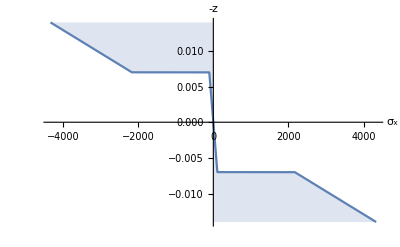

```mathematica
Plot[σx/.{x-> 0,y-> 0,z-> -Z},{Z,-h/2,h/2},Filling->Axis,AxesLabel->{" σ_x ","-z"}]//
AxisFlip
```

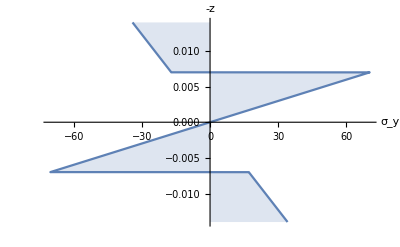

```mathematica
Plot[σy/.{x-> 0,y-> 0,z-> -Z},{Z,-h/2,h/2},Filling->Axis,AxesLabel->{" σ_y ","-z"}]//
AxisFlip
```

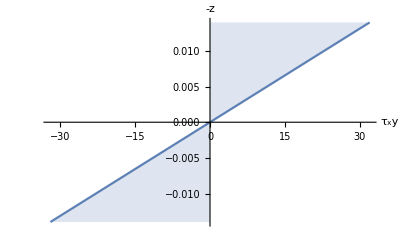

```mathematica
Plot[τxy/.{x-> a/2,y-> -b/2,z-> -Z},{Z,-h/2,h/2},Filling->Axis,AxesLabel->{" τ_xy ","-z"}]//
AxisFlip
```

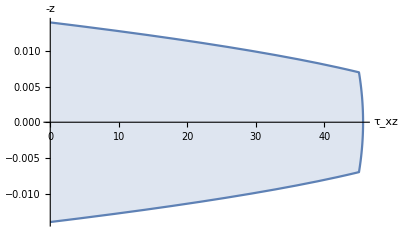

```mathematica
Plot[τxz/.{x-> -a/2,y-> 0,z-> -Z},{Z,-h/2,h/2},Filling->Axis,AxesLabel->{" τ_xz ","-z"}]//
AxisFlip
```

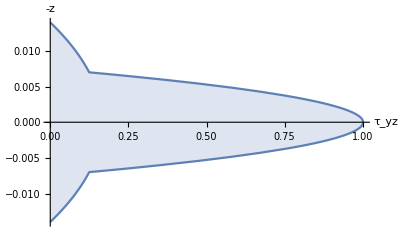

```mathematica
Plot[τyz/.{x-> 0,y->-b/2,z-> -Z},{Z,-h/2,h/2},Filling->Axis,AxesLabel->{" τ_yz ","-z"}]//
AxisFlip
```

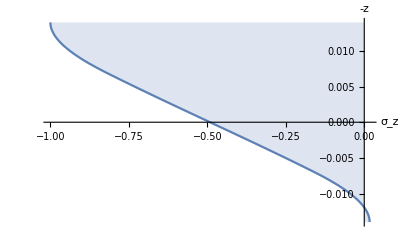

```mathematica
Plot[σz/.{x-> 0,y->0,z-> -Z},{Z,-h/2,h/2},Filling->Axis,AxesLabel->{" σ_z ","-z"}]//
AxisFlip
```

## Chapter 4: Solution Steps using Comsol

#### 1) Define the parameters

#### 2) Orthotropic Material Selection

#### 3) Layered Definition and Visualization

#### 4) Define the Geometry

#### 5) Defining the boundary condition depending on the type of plate problem (CCFF,SSCC, SSFF)

#### 6) Meshing

## Chapter 5: Visualization of Deflection along x and y, In-plane stresses, Out-of-plane stresses and contour plots.

#### SSFF

#### Deflection in x

#### Deflection in y

#### Contour Plot showing locations of high deflection

#### Variation of stress through the thickness of the laminate (In-plane stresses)

#### Variation of σyy through the thickness of the laminate (In-plane stresses)

#### Contour Plot for in-plane stress σxx through the thickness of the laminate

#### Out Of Plane Stresses

## Chapter 6: Results and Comparison

Summarizing the results obtained from both COMSOL Multiphysics 6.0 & Ritz Method and comparing them in an excel sheet, we have the following differences for w, σx , σy,τxy,τxz,τyz,σz respectively:

## Chapter 7: Conclusion

From the results observed, we discovered that the value produced from utilizing the Ritz method are similar to the values produced  by comsol with the exception of the in-plane stress τxy. This could be due to various issues, an example of which as the number of fineness of the mesh used in the comsol simulation. We utilized the thin-plate theory while carrying out finite element modelling in comsol.

## Chapter 8: Mathematica Ritz Package

#### SSFF

```mathematica
BeginPackage["defsf`"]

defsf::usage="Defines the failure properties of a lamina.";
Begin["`Private`"];

defsf[x_,y_,z_,θθ_,th_,Dim_]:=Module[{Sigmaz,σz,Tauyz,τyz,Tauxz,τxz,Sigmax,Sigmay,Sigmaxy,E11,Mpr,E22,G12,ν12,q,ν21,nt,a,b,h,t,Q11,Q22,Q12,Q66,Q,R,T,Qb,zz,DD,D11,D12,D16,D22,D26,D66,n,w,coefw,Nw,Cw,ud1,nu,sol,Mx,My,Mxy,σx,σy,σxy,κ,Intrec,ψ,ψx,ψxx,ψy,ψxy,ψyy,CW,F,K,wxx,wxxx,wxxxx,wxy,wxxy,wyy,wyyy,wxyy,wxxyy,wyyyy,wx,wy},
Mpr={200*10^9,10*10^9,30*10^9,0.2};
E11=Mpr[[1]];
E22=Mpr[[2]];
G12=Mpr[[3]];
ν12=Mpr[[4]];
ν21=ν12*E22/E11;
a=Dim[[1]];
b=Dim[[2]];
h=Dim[[3]];
q=Dim[[4]];

nt=Length[th];
t=h/nt;(*  This code "Intrec" is to evaluate the exact integral of polynomials quickly*)
Intrec[f_,a_,b_]:=Module[{coeff,ii,jj,i,j},coeff=CoefficientList[f,{x,y}];{ii,jj}=Dimensions[coeff];Sum[coeff[[i,j]] ((a/2)^i-(-a/2)^i)/i ((b/2)^j-(-b/2)^j)/j,{i,1,ii},{j,1,jj}]];
(* Compute elements of Qb and D  *)
Q11=E11*1/(1-ν12 ν21);Q22=E22*1/(1-ν12 ν21);Q12=(ν12 *E22)/(1-ν12 ν21);Q66=G12;
Q={{Q11,Q12,0},{Q12,Q22,0},{0,0,Q66}};
T[θ_]:={{Cos[θ]^2,Sin[θ]^2,2 Sin[θ]  Cos[θ]},{Sin[θ]^2,Cos[θ]^2,-2  Sin[θ]  Cos[θ]},{-Sin[θ]  Cos[θ],Sin[θ]  Cos[θ],Cos[θ]^2-Sin[θ]^2}} ;
R=({
 {1, 0, 0},
 {0, 1, 0},
 {0, 0, 2}
});
Qb[θ_]:=Inverse[T[θ]].Q.R.T[θ].Inverse[R];
zz=Range[-h/2,h/2,t];
DD=Table[0,{i,1,3},{j,1,3}];
Do[DD[[i,j]]=1/3 Sum[(Qb[th[[k]]][[i,j]] )  (zz[[k+1]]^3-zz[[k]]^3),{k,1,nt}],{i,1,3},{j,1,3}];
D11=DD[[1,1]];D12=DD[[1,2]];D16=DD[[1,3]];D22=DD[[2,2]];D26=DD[[2,3]];D66=DD[[3,3]];


(* Assume approximationg polynomials that satisfy geometric bcs *)
n=5;
w=(x^2-a^2/4 )  Sum[Cw[i,j]x^(2i) y^(2j) ,{i,0,n},{j,0,n}];




coefw=Cases[Cases[Variables[w],Except[x]],Except[y]];
Nw=Length[coefw];
w=Simplify[w/.Table[coefw[[i]]-> Cw[i],{i,1,Nw}]];
(* Generate approximationg polynomials and their corresponding coefficients *)
Do[ψ[i]=Coefficient[w,Cw[i]],{i,1,Nw}];
Do[ψx[i]=Simplify[D[ψ[i],x]],{i,1,Nw}];
Do[ψy[i]=Simplify[D[ψ[i],y]],{i,1,Nw}];
(* Differentiate approximationg polynomials as requied by K elements *)
Do[ψxx[i]=Simplify[D[ψ[i],{x,2}]],{i,1,Nw}];
Do[ψyy[i]=Simplify[D[ψ[i],{y,2}]],{i,1,Nw}];
Do[ψxy[i]=Simplify[D[D[ψ[i],{x,1}],{y,1}]],{i,1,Nw}];
(* Initialize matrix K and the force vector F *)
K=Table[0,{i,1,Nw},{j,1,Nw}];
F=Table[0,{i,1,Nw}];
(* Evaluate the components of the matrix K *)
Do[K[[i,j]]=Intrec[(ψxx[j](D11 ψxx[i]+D12 ψyy[i]+2D16 ψxy[i])+ψyy[j](D22 ψyy[i]+D12 ψxx[i]+2D26 ψxy[i])+ψxy[j](4D66 ψxy[i]+2D16 ψxx[i]+2D26 ψyy[i])),a,b],{i,1,Nw},{j,1,Nw}];
Do[F[[i]]=Intrec[q ψ[i],a,b],{i,1,Nw}];
(* Solve for polynomil coefficients *)
CW=Table[Cw[i],{i,1,Nw}];
sol=Solve[K.CW==F,CW];
w=w/.sol[[1]];
wxx=D[w,{x,2}];
wyy=D[w,{y,2}];
wxy=D[D[w,x],y];
wx=D[w,x];wy=D[w,y];
wxx=D[wx,x];wxy=D[wx,y];wxxx=D[wxx,x];
wyy=D[wy,y];wyyy=D[wyy,y];wxxy=D[wxx,y];wxyy=D[wxy,y];
wxxxx=D[wxxx,x];wxxyy=D[wxxy,y];wyyyy=D[wyyy,y];
(* The mnth terms of wthe bending moments *)
Mx=-(D11 wxx+D12 wyy);
My=-(D12 wxx+D22 wyy);
Mxy=-2 D66 wxy;
(* Compute curvatures *)
κ={-wxx,-wyy,-2wxy};
(* Compute stresses *)
Do[{σx[k],σy[k],σxy[k]}=Qb[th[[k]]].(z κ),{k,1,nt}];
Sigmax=Piecewise[Table[{σx[k],zz[[k]]<= z<=zz[[k+1]]},{k,1,nt}]];
Sigmay=Piecewise[Table[{σy[k],zz[[k]]<= z<=zz[[k+1]]},{k,1,nt}]];
Sigmaxy=Piecewise[Table[{σxy[k],zz[[k]]<= z<=zz[[k+1]]},{k,1,nt}]];
τxz[0]=0;
Do[τxz[k]=-Integrate[D[σx[k],x]+D[σxy[k],y],{z,zz[[k]],z}]+(τxz[k-1]/.z-> zz[[k]]),{k,1,nt}];
Tauxz=Piecewise[Table[{τxz[k],zz[[k]]<= z<=zz[[k+1]]},{k,1,nt}]];
τyz[0]=0;
Do[τyz[k]=-Integrate[D[τxy[k],x]+D[σy[k],y],{z,zz[[k]],z}]+(τyz[k-1]/.z-> zz[[k]]),{k,1,nt}];
Tauyz=Piecewise[Table[{τyz[k],zz[[k]]<= z<=zz[[k+1]]},{k,1,nt}]];
σz[0]=-q;
Do[σz[k]=-Integrate[D[τxz[k],x]+D[τyz[k],y],{z,zz[[k]],z}]+(σz[k-1]/.z-> zz[[k]]),{k,1,nt}];
Sigmaz=Piecewise[Table[{σz[k],zz[[k]]<= z<=zz[[k+1]]},{k,1,nt}]];


{w,Sigmax,Sigmay,Sigmaxy,Tauxz,Tauyz,Sigmaz}
]
               
End[]

EndPackage[]
```

## References

1- Dr hussain Lectures for CE-625
2-Comsol videos from comsol official website. (https://www.comsol.com)